```mathematica
Style["First we see the NDSolve solution",20]
```

First we see the NDSolve solution

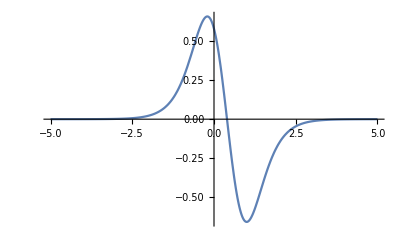

{{y→InterpolatingFunction[{{…, -5., 5., …}, {0., 10.}}, <>]}}

-Graphics3D-

```mathematica
Clear[eq,y,t,u,wave,ci,cc,dx,dt,x,k,tf]
(*Defining variables*)
wave={};(*the inicial wave form as a sum of independent waves*)
xi=-5;(*spacial range*)
xf=5;
ti=0;(*temporal range*)
tf=10;
u=0.1;(*parameters of the equation*)
k=0.5;
dx=0.08;(*parameters of the solution*)
dt=dx^2/2;
Do[
AppendTo[wave,Sech[(2π*x)/xf]^(2n)-Sech[(2π*x-xf)/xf]^(2n)]
,{n,1,10}](*Constructing the waveform*)
(*Solving the equation*)
eq:=D[y[x,t],t]+k*y[x,t]*D[y[x,t],x]==u*D[y[x,t],{x,2}];
ci:=y[x,ti]==wave[[2]];
cc:=y[xi,t]==y[xf,t];
sis={eq,ci,cc};
Plot[wave[[1]],{x,xi,xf},PlotRange->All]
NDSolve[sis,y,{x,xi,xf},{t,ti,tf},MaxSteps->100000,MaxStepSize->{dx,dt}]
sol=y/.%[[1]];
Plot3D[sol[x,t],{x,xi,xf},{t,ti,tf},PlotRange->{-2,2},ImageSize->600]
an1=Animate[Graphics[Plot[sol[x,t],{x,xi,xf},ImageSize->600,PlotRange->1]],{t,ti,tf}]
t=tf;
im2=Plot[sol[x,t],{x,xi,xf},ImageSize->600,PlotRange->All,AxesOrigin->{0,0}];
t=ti;
im2i=Plot[sol[x,t],{x,xi,xf},ImageSize->600,PlotRange->All,AxesOrigin->{0,0}];
```

```mathematica
Style["Solving with Runge Kutta method(we can choose between the first 4 orders of the method)",20]
```

Solving with Runge Kutta method(we can choose between the first 4 orders of the method)

```mathematica
Clear[f,x,te,y,yy,y0,t,Y,M,ff,fj,NN,w,Y0,xn,tn,X,T,RK,Eqn,nx,a,b,tf,dt,F,a1,a2,tff,krk,krk1,krk2,MM,krk3,krk4,XX,aa1,aa2,W]
(*defining variables*)
X={};
T={};
NN=50;(*number of temporal and spatial partitions*)
xn:=(xf-xi)/(NN-1);(*spatial step*)
tn:=(tf-ti)/(NN-1);(*temporal step*)
aa1=0.5;(*parameters of the method in all orders*)
aa2=1-aa1;
a1=2.5/6;
a2=3/6;
a3=1-a1-a2;
p=0.6;
q=1-p;
r=3;
s=8;
nx=0;
ord=1;(*the order of the method*)

xi=-5;(*spatial range*)
xf=5;
ti=0;(*temporal range*)
tf=10;
u=0.1;
k=0.1;
dx=0.08;
dt=dx^2/2;
w=Y0;(*inicial state*)
W={w};(*the solution*)
dt=(tf-ti)/(NN-1.);
tn=dt;
t=ti;
X=Table[x,{x,xi,xf,xn}];
T=Table[t,{t,ti,tf,tn}];


f[x_,t_]:=u*D[y[x,t],{x,2}]-k*y[x,t]*D[y[x,t],x];(*the burguers equation*)

M={};
fj={};
t=ti;
Do[y0[x]=wave[[1]],{x,xi,xf,xn}];
Y0=Table[y0[x],{x,xi,xf,xn}];
Y=Y0;
Clear[t];
Y=Table[y[x,t],{x,xi,xf,xn}];

(*Runge Kutta method in 4 orders*)
F[t_,w_,dt_]:=Module[{},
(M.w)
];
RK[1][F_,t_,w_,dt_]:=Module[{},
krk=F[t,w,dt];
w+krk*dt

];
RK[2][F_,t_,w_,dt_]:=Module[{},
krk1=F[t,w,dt/2];

krk2=F[t+dt,w+krk1*dt,dt/2];

w+(aa1*krk1+aa2*krk2)*dt
]; 
RK[3][F_,t_,w_,dt_]:=Module[{},

krk1=F[t,w,dt];
krk2=F[t+dt,w+krk1*dt/2,dt];
krk3=F[t+r*dt,w+s*krk2*dt/2+(r-s)*krk1*dt/2,dt];
w+(a1*krk1+a2*krk2+a3*krk3)*dt
];
RK[4][F_,t_,w_,dt_]:=Module[{},
krk1=F[t,w,dt];
krk2=F[t+dt,w+krk1*dt,dt];
krk3=F[t+dt,w+krk2*dt,dt];
krk4=F[t+dt,w+krk3*dt,dt];
w+(krk1+2*krk2+2krk3+krk4)*dt/6];



(*Constructing the matrix representing the temporal derivative*)


MM={};
t=ti;
Do[
M=Table[0,{i,1,NN},{j,1,NN}];
Do[
Do[
If[i==j,M[[i,j]]=-2*u/xn^2];
If[i==j+1,M[[i,j]]=u/xn^2-(-k/(2*dx))*w[[j]]];
If[i==j-1,M[[i,j]]=u/xn^2+(-k/(2*dx))*w[[j]]];
If[i==NN&&j==1,M[[i,j]]=u/xn^2+(-k/(2*dx))*w[[j]]];
If[i==1&&j==NN,M[[i,j]]=u/xn^2-(-k/(2*dx))*w[[j]]];
,{i,1,NN}];
,{j,1,NN}];




w=RK[ord][F,t,w,dt];
                t=t+dt;
AppendTo[W,w];
AppendTo[MM,M]
              ,{n,2,NN}];
```

```mathematica
an2=Animate[
ListPlot[W[[i]],Joined->True,DataRange->xf-xi,PlotRange->{-1,1},ImageSize->600],{i,1,NN,1}]
```

```mathematica
ListPlot3D[W,PlotRange->All,ImageSize->600]
```

-Graphics3D-